```mathematica
AppendTo[$Path,"/home/daneel/phystuff/optical_double_well/codes_presvn/mathematica/levelscheme"];
Get["LevelScheme`"];
Potential[x_]:=2.0*V0*(-2*x^2+x^4);
L=3.5;
DiagramOfLevels=Scheme[
             {
            SetOptions[Lev,Thickness-> 0.5,Color-> Black],
             SetOptions[Trans,ArrowType->SquiggleArrow,FillColor-> LightGray],
            
 Lev[Level1z,Solve[Potential[x]==SortedEnergies[[1]],x][[1]][[1]][[2]],Solve[Potential[x]==SortedEnergies[[1]],x][[2]][[1]][[2]],SortedEnergies[[1]]],
             Lev[Level11,Solve[Potential[x]==SortedEnergies[[1]],x][[3]][[1]][[2]],Solve[Potential[x]==SortedEnergies[[1]],x][[4]][[1]][[2]],SortedEnergies[[1]]],

 Lev[Level2z,Solve[Potential[x]==SortedEnergies[[2]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[2]],x][[2]][[1]][[2]],SortedEnergies[[2]]],
             Lev[Level21,Solve[Potential[x]==SortedEnergies[[2]],x][[3]][[1]][[2]],Solve[Potential[x]==SortedEnergies[[2]],x][[4]][[1]][[2]],SortedEnergies[[2]]],

 Lev[Level3z,Solve[Potential[x]==SortedEnergies[[3]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[3]],x][[4]][[1]][[2]],SortedEnergies[[3]]],
            (* Lev[Level31,Solve[Potential[x]==SortedEnergies[[3]],x][[3]][[1]][[2]],Solve[Potential[x]==SortedEnergies[[3]],x][[4]][[1]][[2]],SortedEnergies[[3]]],*)


 Lev[Level4z,Solve[Potential[x]==SortedEnergies[[4]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[4]],x][[4]][[1]][[2]],SortedEnergies[[4]]],
        
 Lev[Level5z,Solve[Potential[x]==SortedEnergies[[5]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[5]],x][[4]][[1]][[2]],SortedEnergies[[5]]],
            





 Lev[Level6z,Solve[Potential[x]==SortedEnergies[[6]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[6]],x][[4]][[1]][[2]],SortedEnergies[[6]]],
        

 Lev[Level7z,Solve[Potential[x]==SortedEnergies[[7]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[7]],x][[4]][[1]][[2]],SortedEnergies[[7]]],


 Lev[Level8z,Solve[Potential[x]==SortedEnergies[[8]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[8]],x][[4]][[1]][[2]],SortedEnergies[[8]]],

 Lev[Level9z,Solve[Potential[x]==SortedEnergies[[9]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[9]],x][[4]][[1]][[2]],SortedEnergies[[9]]],
          

 Lev[Level10z,Solve[Potential[x]==SortedEnergies[[10]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[10]],x][[4]][[1]][[2]],SortedEnergies[[10]]],
        


Lev[Level11z,Solve[Potential[x]==SortedEnergies[[11]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[11]],x][[4]][[1]][[2]],SortedEnergies[[11]]],
  


Lev[Level12z,Solve[Potential[x]==SortedEnergies[[12]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[12]],x][[4]][[1]][[2]],SortedEnergies[[12]]],




Lev[Level13z,Solve[Potential[x]==SortedEnergies[[13]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[13]],x][[4]][[1]][[2]],SortedEnergies[[13]]],








Lev[Level14z,Solve[Potential[x]==SortedEnergies[[14]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[14]],x][[4]][[1]][[2]],SortedEnergies[[14]]],


Lev[Level15z,Solve[Potential[x]==SortedEnergies[[15]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[15]],x][[4]][[1]][[2]],SortedEnergies[[15]]],


Lev[Level16z,Solve[Potential[x]==SortedEnergies[[16]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[16]],x][[4]][[1]][[2]],SortedEnergies[[16]]],


Lev[Level17z,Solve[Potential[x]==SortedEnergies[[17]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[17]],x][[4]][[1]][[2]],SortedEnergies[[17]]],

Lev[Level18z,Solve[Potential[x]==SortedEnergies[[18]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[18]],x][[4]][[1]][[2]],SortedEnergies[[18]]],

Lev[Level19z,Solve[Potential[x]==SortedEnergies[[19]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[19]],x][[4]][[1]][[2]],SortedEnergies[[19]]],

Lev[Level20z,Solve[Potential[x]==SortedEnergies[[20]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[20]],x][[4]][[1]][[2]],SortedEnergies[[20]]],

Lev[Level21z,Solve[Potential[x]==SortedEnergies[[21]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[21]],x][[4]][[1]][[2]],SortedEnergies[[21]]],

Lev[Level22z,Solve[Potential[x]==SortedEnergies[[22]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[22]],x][[4]][[1]][[2]],SortedEnergies[[22]]],

Lev[Level23z,Solve[Potential[x]==SortedEnergies[[23]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[23]],x][[4]][[1]][[2]],SortedEnergies[[23]]],

Lev[Level24z,Solve[Potential[x]==SortedEnergies[[24]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[24]],x][[4]][[1]][[2]],SortedEnergies[[24]]],

Lev[Level25z,Solve[Potential[x]==SortedEnergies[[25]],x][[1]][[1]][[2]],
Solve[Potential[x]==SortedEnergies[[25]],x][[4]][[1]][[2]],SortedEnergies[[25]]],

             Trans[Level1z,0.3,Level2z,0.33],
             Trans[Level21,0.6,Level4z
,2.46],
            
           },
PlotRange-> {{-L,L},{-2.1*V0,4.5*V0}},ImageSize-> 80*{6,3},Frame->True,FrameTicks->{None, Automatic},FontFamily->"Bitstream Vera Sans",FontSize->30
];
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.41 (September 11, 2007)
View color paletteVisit home page

4.

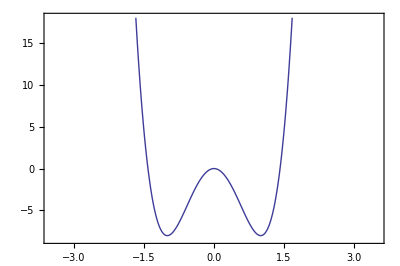

```mathematica
V0
WellGraph=Plot[Potential[x],{x,-L,L},PlotRange-> {-2.1*V0,4.5*V0},Frame->True,Axes->False,AspectRatio-> 2/3, TextStyle->{FontFamily -> "Bitstream Vera Sans Mono", FontSize-> 40} ]
```

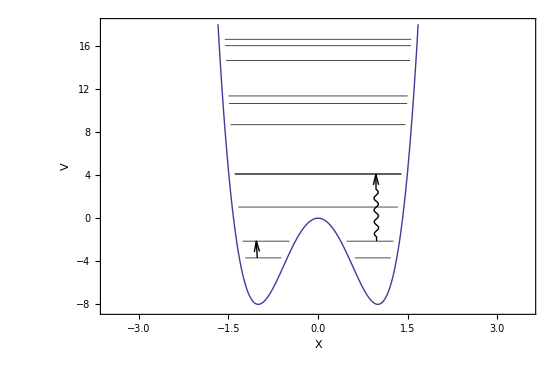

{x→1.42834}

```mathematica
Show[WellGraph,DiagramOfLevels,FrameLabel->{"X","V"}]
```

```mathematica
SortedEnergies={-9.49437,-6.30961,-5.68476,-0.45879,-0.131533,5.54686,6.21968,7.8325,13.0722,13.1073,13.8945,18.3994,20.9508,21.3311,22.2348,25.8682,29.3445,30.7074,31.3562,33.1758,34.6609,39.0028,40.651,41.4109,41.5876,44.0893,49.0141,49.7151,51.2724,51.5144,51.9947,54.2542,59.2786,59.7772,61.5419,62.9136,63.7011,64.9658,68.5113,69.7176,71.2466,72.5017,76.6755,78.5793,80.7102,84.2676,88.5604,90.0181,90.258,90.9184,92.9175,98.3477,99.3277,102.488,103.676,108.333,109.178,110.074,111.279,112.717,116.411,119.589,121.937,123.064,129.278,129.359,134.266,137.88,139.326,147.37,150.682,157.63,162.808,168.686,177.984,178.624,180.616,186.057,191.306,192.769,198.927,202.448,203.33,207.118,210.513,213.965,215.967,216.786,223.333,226.679,229.901,231.75,237.658,241.168,249.459,251.364,262.049,274.033,279.325,298.255,303.591,322.251,330.237,330.895,338.393,343.557,351.147,358.536,359.327,359.437,366.598,368.954,369.989,371.986,378.817,379.385,387.867,389.718,397.171,398.831,401.441,407.269,417.962,420.029,429.906,430.483,448.72,458.598,477.172,519.882,544.649,548.315,566.962,567.624,572.949,575.178,580.282,587.843,594.324,595.183,596.042,602.387,605.596,607.899,615.164,615.518,623.518,626.483,632.939,638.105,643.045,653.712,665.708,666.95,675.168,685.125,694.193,708.565,712.688,732.925,755.445,779.939,782.703,807.474,908.981,911.806,912.501,919.932,925.158,930.901,931.663,932.804,935.182,938.674,938.964,940.915,944.409,950.602,951.737,960.228,960.386,964.911,969.509,971.327,979.703,982.963,990.276,1002.23,1011.74,1029.92,1030.72,1049.18,1100.08,1119.05,1124.55,1143.79,1148.99,1182.13,1205.08,1252.71,1271.65,1281.01,1300.22,1490.57,1509.17,1518.5,1537.27,1839.17,1865.55,1879.68}
```

{-9.49437,-6.30961,-5.68476,-0.45879,-0.131533,5.54686,6.21968,7.8325,13.0722,13.1073,13.8945,18.3994,20.9508,21.3311,22.2348,25.8682,29.3445,30.7074,31.3562,33.1758,34.6609,39.0028,40.651,41.4109,41.5876,44.0893,49.0141,49.7151,51.2724,51.5144,51.9947,54.2542,59.2786,59.7772,61.5419,62.9136,63.7011,64.9658,68.5113,69.7176,71.2466,72.5017,76.6755,78.5793,80.7102,84.2676,88.5604,90.0181,90.258,90.9184,92.9175,98.3477,99.3277,102.488,103.676,108.333,109.178,110.074,111.279,112.717,116.411,119.589,121.937,123.064,129.278,129.359,134.266,137.88,139.326,147.37,150.682,157.63,162.808,168.686,177.984,178.624,180.616,186.057,191.306,192.769,198.927,202.448,203.33,207.118,210.513,213.965,215.967,216.786,223.333,226.679,229.901,231.75,237.658,241.168,249.459,251.364,262.049,274.033,279.325,298.255,303.591,322.251,330.237,330.895,338.393,343.557,351.147,358.536,359.327,359.437,366.598,368.954,369.989,371.986,378.817,379.385,387.867,389.718,397.171,398.831,401.441,407.269,417.962,420.029,429.906,430.483,448.72,458.598,477.172,519.882,544.649,548.315,566.962,567.624,572.949,575.178,580.282,587.843,594.324,595.183,596.042,602.387,605.596,607.899,615.164,615.518,623.518,626.483,632.939,638.105,643.045,653.712,665.708,666.95,675.168,685.125,694.193,708.565,712.688,732.925,755.445,779.939,782.703,807.474,908.981,911.806,912.501,919.932,925.158,930.901,931.663,932.804,935.182,938.674,938.964,940.915,944.409,950.602,951.737,960.228,960.386,964.911,969.509,971.327,979.703,982.963,990.276,1002.23,1011.74,1029.92,1030.72,1049.18,1100.08,1119.05,1124.55,1143.79,1148.99,1182.13,1205.08,1252.71,1271.65,1281.01,1300.22,1490.57,1509.17,1518.5,1537.27,1839.17,1865.55,1879.68}

```mathematica
V0
```

4.